## Constraint Plots

### Plot the limit

```mathematica
(*Function to convert mass, Log[10,epsilon^{2}]   to   mass, epsilon*)
```

```mathematica
DataConvertermine[data_]:=Table[{data[[i,1]],√(10^data[[i,2]])},{i,Length[data]}]
```

```mathematica
Labelslin={"Br(H->2γ_D)=0.1%","Br(H->2γ_D)=1%","Br(H->2γ_D)=5%","Br(H->2γ_D)=10%","Br(H->2γ_D)=20%","Br(H->2γ_D)=40%"}
```

{Br(H->2γ_D)=0.1%,Br(H->2γ_D)=1%,Br(H->2γ_D)=5%,Br(H->2γ_D)=10%,Br(H->2γ_D)=20%,Br(H->2γ_D)=40%}

```mathematica
legendlin=SwatchLegend[{Darker[Cyan,0.2],Darker[Blue,0.2],Darker[Green,0.2],Darker[Yellow,0.2],Darker[Orange,0.2],Darker[Red,0.2]},Labelslin,LegendMarkerSize->{{15,15}},LabelStyle->{Italic,16},LegendMarkers->{"Line"}];
```

```mathematica
listbr01 = Import["/Users/Alfredo/Desktop/limite_DarkSUSY_2018/Limit_epsvsmass_BrHtoGamD_01_2018.dat"];
listbr1 =   Import["/Users/Alfredo/Desktop/limite_DarkSUSY_2018/Limit_epsvsmass_BrHtoGamD_1_2018.dat"];
listbr5 =   Import["/Users/Alfredo/Desktop/limite_DarkSUSY_2018/Limit_epsvsmass_BrHtoGamD_5_2018.dat"];
listbr10 = Import["/Users/Alfredo/Desktop/limite_DarkSUSY_2018/Limit_epsvsmass_BrHtoGamD_10_2018.dat"];
listbr20 = Import["/Users/Alfredo/Desktop/limite_DarkSUSY_2018/Limit_epsvsmass_BrHtoGamD_20_2018.dat"];
listbr40 = Import["/Users/Alfredo/Desktop/limite_DarkSUSY_2018/Limit_epsvsmass_BrHtoGamD_40_2017.dat"];
```

```mathematica
plotLimEpsilonvsmass = Legended[ListLogLogPlot[{DataConvertermine[DeleteCases[listbr01,{Null,Null}]],DataConvertermine[DeleteCases[listbr1,{Null,Null}]],DataConvertermine[DeleteCases[listbr5,{Null,Null}]],DataConvertermine[DeleteCases[listbr10,{Null,Null}]],DataConvertermine[DeleteCases[listbr20,{Null,Null}]],DataConvertermine[DeleteCases[listbr40,{Null,Null}]]}, Joined->True,PlotRange->{{0.25,9.0},{0.4 10^-7,0.1 10^-1}},ImageSize->500,AspectRatio->1.0,TicksStyle->Directive[FontSize->18],Frame->True,FrameLabel->{"m_γD[GeV]","Kinetic Mixing Parameter ϵ"},RotateLabel->True,BaseStyle->{FontSize->18},PlotStyle->{Darker[Cyan,0.2],Darker[Blue,0.2],Darker[Green,0.2],Darker[Yellow,0.2],Darker[Orange,0.2],Darker[Red,0.2]}],Placed[legendlin,{0.72,0.65}]]
```

```mathematica
Export["/Users/Alfredo/Desktop/limite_DarkSUSY_2017/Limit_DarkPhoton_Epsilon_vs_mass.pdf",plotLimEpsilonvsmass]
```

```mathematica
legendlin2=SwatchLegend[{Darker[Cyan,0.2],Darker[Blue,0.2],Darker[Green,0.2],Darker[Yellow,0.2],Darker[Orange,0.2],Darker[Red,0.2]},Labelslin,LegendMarkerSize->{{15,15}},LabelStyle->{Italic,9},LegendMarkers->{"Line"}]
```

```mathematica
(* The plot above to be combined with the other experiment limits *)
```

```mathematica
plotLimEpsilonvsmass2 = Legended[ListLogLogPlot[{DataConvertermine[DeleteCases[listbr01,{Null,Null}]],DataConvertermine[DeleteCases[listbr1,{Null,Null}]],DataConvertermine[DeleteCases[listbr5,{Null,Null}]],DataConvertermine[DeleteCases[listbr10,{Null,Null}]],DataConvertermine[DeleteCases[listbr20,{Null,Null}]],DataConvertermine[DeleteCases[listbr40,{Null,Null}]]}, Joined->True,PlotRange->{{0.25,9.0},{0.4 10^-7,0.1 10^-1}},ImageSize->500,AspectRatio->1.0,TicksStyle->Directive[FontSize->18],Frame->True,FrameLabel->{"m_γD[GeV]","Kinetic Mixing Parameter ϵ"},RotateLabel->True,BaseStyle->{FontSize->18},PlotStyle->{Darker[Cyan,0.2],Darker[Blue,0.2],Darker[Green,0.2],Darker[Yellow,0.2],Darker[Orange,0.2],Darker[Red,0.2]}],Placed[legendlin2,{0.87,0.18}]]
```

General::stop: Further output of ListLogLogPlot :: lpn will be suppressed during this calculation.

```mathematica
plotLimEpsilonvsmass2 = Legended[ListLogLogPlot[{DataConvertermine[DeleteCases[listbr01,{Null,Null}]],DataConvertermine[DeleteCases[listbr1,{Null,Null}]],DataConvertermine[DeleteCases[listbr5,{Null,Null}]],DataConvertermine[DeleteCases[listbr10,{Null,Null}]],DataConvertermine[DeleteCases[listbr20,{Null,Null}]],DataConvertermine[DeleteCases[listbr40,{Null,Null}]]}, Joined->True,PlotRange->{{0.25,9.0},{0.4 10^-7,0.1 10^-1}},ImageSize->500,AspectRatio->1.0,TicksStyle->Directive[FontSize->18],Frame->True,FrameLabel->{"m_γD[GeV]","Kinetic Mixing Parameter ϵ"},RotateLabel->True,BaseStyle->{FontSize->18},PlotStyle->{Darker[Cyan,0.2],Darker[Blue,0.2],Darker[Green,0.2],Darker[Yellow,0.2],Darker[Orange,0.2],Darker[Red,0.2]}],Placed[legendlin,{0.72,0.65}]]
```

```mathematica
DataConvertertest[data_]:=Table[{data[[i,1]],√(10^data[[i,2]])},{i,1,Length[data]}]
```

{{},{0.25,-10.},{0.26,-10.06},{0.27,-10.11},{0.28,-10.15},{0.29,-10.2},{0.3,-10.24},{0.31,-10.24},{0.32,-10.3},{0.33,-10.3},{0.34,-10.36},{0.35,-10.39},{0.36,-10.4},{0.37,-10.4},{0.38,-10.42},{0.39,-10.42},{0.4,-10.45},{0.41,-10.49},{0.42,-10.49},{0.43,-10.54},{0.44,-10.56},{0.45,-10.56},{0.46,-10.56},{0.47,-10.6},{0.48,-10.6},{0.49,-10.6},{0.5,-10.6},{0.51,-10.61},{0.52,-10.67},{0.53,-10.68},{0.54,-10.68},{0.55,-10.68},{0.56,-10.68},{0.57,-10.68},{0.58,-10.73},{0.59,-10.73},{0.6,-10.73},{0.61,-10.73},{0.62,-10.73},{0.63,-10.68},{0.64,-10.73},{0.65,-10.68},{0.66,-10.68},{0.67,-10.6},{0.68,-10.4},{0.69,-10.4},{0.7,-4.},{0.71,-4.},{0.72,-4.},{0.73,-4.},{0.74,-4.},{0.75,-4.}}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

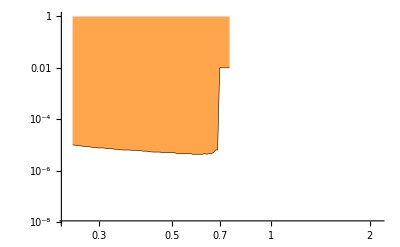

```mathematica
CMS201401= Import["/Users/Alfredo/Desktop/limite_DarkSUSY_2018/Limit_epsvsmass_BrHtoGamD_01_90CL_2018.dat","Table"]
CMS201401plot = ListLogLogPlot[DataConvertertest[CMS201401],Joined->True,PlotStyle->{(*Lighter[Orange,0.3]*)Black,Thickness[0.001]},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Orange,0.3]],PlotRange->{10^-8,1}]
```

{{},{0.25,-10.56},{0.3,-10.8},{0.35,-10.96},{0.4,-11.06},{0.45,-11.14},{0.5,-11.2},{0.55,-11.3},{0.6,-11.36},{0.65,-11.4},{0.7,-11.4},{0.7,-11.4},{0.71,-11.4},{0.72,-11.4},{0.73,-11.4},{0.74,-11.4},{0.75,-11.4},{0.76,-11.4},{0.77,-11.4},{0.78,-11.},{0.79,-11.4},{0.8,-11.5},{0.81,-11.52},{0.82,-11.58},{0.83,-11.6},{0.84,-11.6},{0.85,-11.6},{0.85,-11.6},{0.9,-11.6},{0.95,-11.68},{1.,-11.8},{1.,-11.8},{1.01,-11.8},{1.02,-4.},{1.03,-11.8},{1.04,-11.82},{1.05,-11.82},{1.06,-11.86},{1.07,-11.86},{1.08,-11.86},{1.09,-11.86},{1.1,-11.9},{1.11,-11.9},{1.12,-11.9},{1.13,-11.86},{1.14,-11.86},{1.15,-11.82},{1.16,-11.82},{1.17,-11.82},{1.18,-11.86},{1.19,-11.9},{1.2,-11.92},{1.2,-11.92},{1.25,-12.},{1.3,-12.01},{1.35,-12.01},{1.4,-11.97},{1.45,-12.04},{1.5,-12.15},{1.55,-12.16},{1.6,-12.2},{1.65,-12.2},{1.7,-12.22},{1.75,-12.22},{1.8,-12.2},{1.85,-12.2},{1.9,-12.2},{1.95,-12.22},{2.,-12.32},{2.,-12.32},{2.1,-12.43},{2.2,-12.48},{2.3,-12.48},{2.4,-12.43},{2.5,-12.6},{2.6,-12.6},{2.7,-12.64},{2.8,-12.67},{2.9,-12.7},{3.,-12.6},{3.1,-12.52},{3.2,-12.64},{3.3,-12.8},{3.4,-12.85},{3.5,-12.88},{3.5,-12.88},{3.53,-12.88},{3.56,-12.88},{3.59,-12.88},{3.62,-12.88},{3.65,-12.88},{3.68,-12.88},{3.71,-12.88},{3.74,-12.88},{3.77,-12.88},{3.8,-12.92},{3.83,-12.92},{3.86,-12.92},{3.89,-12.92},{3.92,-12.94},{3.95,-12.94},{3.98,-12.94},{4.01,-12.94},{4.04,-12.94},{4.07,-12.94},{4.1,-12.96},{4.13,-12.96},{4.16,-12.96},{4.19,-12.96},{4.22,-12.96},{4.25,-13.},{4.28,-13.},{4.31,-13.},{4.34,-13.},{4.37,-13.},{4.4,-13.},{4.43,-13.},{4.46,-13.},{4.49,-13.},{4.52,-13.},{4.55,-13.01},{4.58,-13.01},{4.61,-13.06},{4.64,-13.06},{4.67,-13.06},{4.7,-13.06},{4.73,-13.06},{4.76,-13.06},{4.79,-13.06},{4.82,-13.06},{4.85,-13.06},{4.88,-13.11},{4.91,-13.11},{4.94,-13.12},{4.97,-13.12},{5.,-13.12},{5.,-13.12},{5.05,-13.12},{5.1,-13.15},{5.15,-13.15},{5.2,-13.15},{5.25,-13.15},{5.3,-13.2},{5.35,-13.2},{5.4,-13.2},{5.45,-13.2},{5.5,-13.2},{5.55,-13.24},{5.6,-13.24},{5.65,-13.27},{5.7,-13.28},{5.75,-13.28},{5.8,-13.3},{5.85,-13.3},{5.9,-13.3},{5.95,-13.3},{6.,-13.34},{6.05,-13.34},{6.1,-13.34},{6.15,-13.34},{6.2,-13.34},{6.25,-13.36},{6.3,-13.4},{6.35,-13.4},{6.4,-13.4},{6.45,-13.4},{6.5,-13.4},{6.55,-13.45},{6.6,-13.45},{6.65,-13.45},{6.7,-13.45},{6.75,-13.48},{6.8,-13.48},{6.85,-13.48},{6.9,-13.48},{6.95,-13.48},{7.,-13.53},{7.05,-13.53},{7.1,-13.53},{7.15,-13.53},{7.2,-13.53},{7.25,-13.53},{7.3,-13.58},{7.35,-13.58},{7.4,-13.58},{7.45,-13.6},{7.5,-13.6},{7.55,-13.6},{7.6,-13.6},{7.65,-13.6},{7.7,-13.6},{7.75,-13.62},{7.8,-13.62},{7.85,-13.66},{7.9,-13.66},{7.95,-13.66},{8.,-13.66},{8.05,-13.66},{8.1,-13.66},{8.15,-13.66},{8.2,-13.69},{8.25,-13.72},{8.3,-13.72},{8.35,-13.72},{8.4,-13.72},{8.45,-13.72},{8.5,-13.72},{8.55,-13.72},{8.6,-13.76},{8.65,-13.76},{8.7,-13.76},{8.75,-13.79},{8.8,-13.79},{8.85,-13.8},{8.9,-13.8},{8.95,-13.8},{9.,-13.8}}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

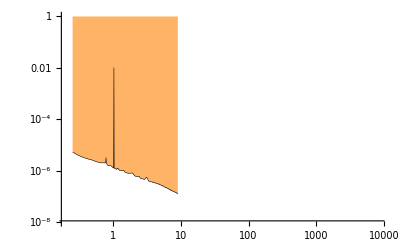

```mathematica
CMS20141= Import["/Users/Alfredo/Desktop/limite_DarkSUSY_2018/Limit_epsvsmass_BrHtoGamD_1_90CL_2018.dat","Table"]
CMS20141plot = ListLogLogPlot[DataConvertertest[CMS20141],Joined->True,PlotStyle->{(*Lighter[Orange,0.4]*)Black,Thickness[0.001]},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Orange,0.4]],PlotRange->{10^-8,1}]
```

```mathematica
CMS20145= Import["/Users/Alfredo/Desktop/limite_DarkSUSY_2018/Limit_epsvsmass_BrHtoGamD_5_90CL_2018.dat","Table"]
CMS20145plot = ListLogLogPlot[DataConvertertest[CMS20145],Joined->True,PlotStyle->{(*Green*)(*Lighter[Orange,0.5]*)Black,Thickness[0.001]},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],(*Green*)Lighter[Orange,0.5]],PlotRange->{10^-8,1}]
```

```mathematica
CMS201410= Import["/Users/Alfredo/Desktop/limite_DarkSUSY_2018/Limit_epsvsmass_BrHtoGamD_10_90CL_2018.dat","Table"]
CMS201410plot = ListLogLogPlot[DataConvertertest[CMS201410],Joined->True,PlotStyle->{(*Yellow*)(*Lighter[Orange,0.6]*)Black,Thickness[0.001]},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity], (*Yellow*)Lighter[Orange,0.6]],PlotRange->{10^-8,1}]
```

```mathematica
CMS201420= Import["/Users/Usuario/Desktop/limite_DarkSUSY_2018/Limit_epsvsmass_BrHtoGamD_20_90CL_2018.dat","Table"]
CMS201420plot = ListLogLogPlot[DataConvertertest[CMS201420],Joined->True,PlotStyle->{Orange,Thickness[0.001]},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity], Orange],PlotRange->{10^-8,1}]
```

```mathematica
Labelslin={"Br(H->2γ_D)=0.1%","Br(H->2γ_D)=1%","Br(H->2γ_D)=5%","Br(H->2γ_D)=10%","Br(H->2γ_D)=20%","Br(H->2γ_D)=40%"}
```

{Br(H->2γ_D)=0.1%,Br(H->2γ_D)=1%,Br(H->2γ_D)=5%,Br(H->2γ_D)=10%,Br(H->2γ_D)=20%,Br(H->2γ_D)=40%}

```mathematica
legendlin=SwatchLegend[{Purple,Blue,Green,Yellow,Orange,Red},Labelslin,LegendMarkerSize->{{15,15}},LabelStyle->{Italic,14},LegendMarkers->{Graphics[Rectangle[]]}];
```

```mathematica
CMS201440= Import["/Users/Alfredo/Desktop/limite_DarkSUSY_2018/Limit_epsvsmass_BrHtoGamD_40_90CL_2017.dat","Table"]
(*CMS201440plot = Legended[ListLogLogPlot[DataConvertertest[CMS201440],Joined->True,PlotStyle->{(*Lighter[Orange,0.7]*)Black,Thickness[0.001]},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity], Lighter[Orange,0.7]],PlotRange->{10^-11,1}],Placed[legendlin,{0.72,0.20}]]*)
CMS201440plot =ListLogLogPlot[DataConvertertest[CMS201440],Joined->True,PlotStyle->{(*Lighter[Orange,0.7]*)Black,Thickness[0.001]},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity], Lighter[Orange,0.7]],PlotRange->{10^-11,1}]
```

{{},{0.25,-11.36},{0.3,-11.6},{0.35,-11.75},{0.4,-11.86},{0.45,-11.95},{0.5,-12.04},{0.55,-12.13},{0.6,-12.2},{0.65,-12.26},{0.7,-12.32},{0.7,-12.32},{0.71,-12.32},{0.72,-12.36},{0.73,-12.36},{0.74,-12.36},{0.75,-12.39},{0.76,-12.4},{0.77,-12.4},{0.78,-12.4},{0.79,-12.4},{0.8,-12.43},{0.81,-12.43},{0.82,-12.48},{0.83,-12.48},{0.84,-12.48},{0.85,-12.48},{0.85,-12.48},{0.9,-12.46},{0.95,-12.52},{1.,-12.64},{1.,-12.64},{1.01,-12.64},{1.02,-12.55},{1.03,-12.67},{1.04,-12.67},{1.05,-12.7},{1.06,-12.7},{1.07,-12.7},{1.08,-12.7},{1.09,-12.7},{1.1,-12.72},{1.11,-12.75},{1.12,-12.75},{1.13,-12.72},{1.14,-12.7},{1.15,-12.67},{1.16,-12.67},{1.17,-12.67},{1.18,-12.7},{1.19,-12.76},{1.2,-12.77},{1.2,-12.77},{1.3,-12.88},{1.4,-12.82},{1.5,-13.},{1.6,-13.06},{1.7,-13.11},{1.8,-13.1},{1.9,-13.06},{2.,-13.18},{2.,-13.18},{2.1,-13.3},{2.2,-13.34},{2.3,-13.34},{2.4,-13.32},{2.5,-13.45},{2.6,-13.48},{2.7,-13.48},{2.8,-13.53},{2.9,-13.57},{3.,-13.48},{3.1,-13.42},{3.2,-13.53},{3.3,-13.66},{3.4,-13.72},{3.5,-13.76},{3.5,-13.76},{3.6,-13.76},{3.7,-13.76},{3.8,-13.79},{3.9,-13.8},{4.,-13.8},{4.1,-13.84},{4.2,-13.84},{4.3,-13.85},{4.4,-13.91},{4.5,-13.91},{4.6,-13.91},{4.7,-13.96},{4.8,-13.96},{4.9,-13.96},{5.,-14.},{5.,-14.},{5.1,-14.},{5.2,-14.02},{5.3,-14.08},{5.4,-14.1},{5.5,-14.1},{5.6,-14.13},{5.7,-14.13},{5.8,-14.18},{5.9,-14.2},{6.,-14.2},{6.1,-14.2},{6.2,-14.24},{6.3,-14.24},{6.4,-14.29},{6.5,-14.29},{6.6,-14.29},{6.7,-14.32},{6.8,-14.35},{6.9,-14.38},{7.,-14.38},{7.1,-14.4},{7.2,-14.4},{7.3,-14.44},{7.4,-14.46},{7.5,-14.47},{7.6,-14.48},{7.7,-14.48},{7.8,-14.48},{7.9,-14.5},{8.,-14.53},{8.1,-14.56},{8.2,-14.56},{8.3,-14.56},{8.4,-14.6},{8.5,-14.6},{8.6,-14.6},{8.7,-14.64},{8.8,-14.64},{8.9,-14.67},{9.,-14.67}}

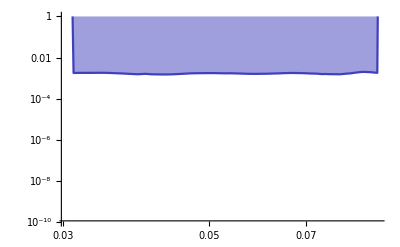

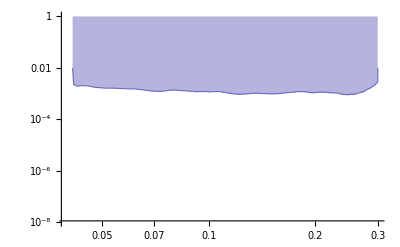

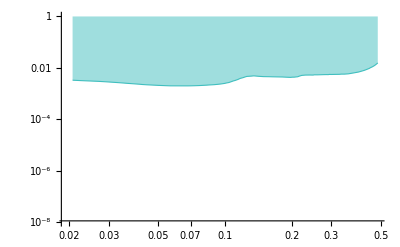

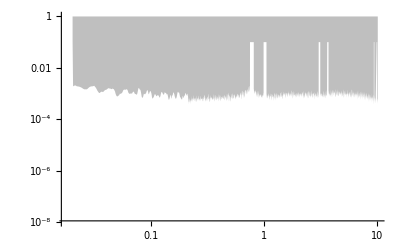

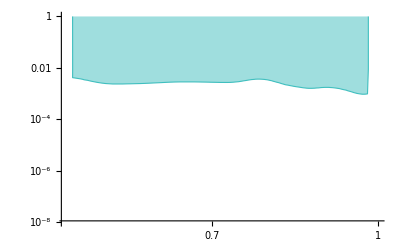

```mathematica
SetDirectory[NotebookDirectory[]];


mμ=0.1057 GeV;
me=0.000511*GeV;
α=1/137.0;
inCM={GeV->5.0677 10^13/CM};
inSec={GeV->1.51926778 10^24/seconds};
SaveRdataMod=Import["data/SaveRdataMod.txt","Table"];

Rhad[m_]:=If[m<.36,0,Interpolation[SaveRdataMod,InterpolationOrder->1][m]]

electronWidthFunction[mA_]:=√(1-4 me^2/(mA^2*GeV^2));
muonWidthFunction[mA_]:=√Max[1-4 mμ^2/(mA^2*GeV^2),0]
totalWidthFunction[mA_]:=√(1-4 me^2/(mA^2*GeV^2))+√Max[1-4 mμ^2/(mA^2*GeV^2),0]  (1+Rhad[mA])
muonfraction[mA_]:=muonWidthFunction[mA]/totalWidthFunction[mA]
SigmaAOnShell[Ecm_,alpha_,alphaD_,epsilon_,mL_,mA_,thetamin_]:=0.3894*10^(-3+15)*4*π*epsilon^2*alpha^2*1/Ecm^2*(1-mA^2/Ecm^2)*((2+(4*mA^2)/(Ecm^2*(1-mA^2/Ecm^2)^2))*Log[2/thetamin]-1+1/8*(2-(4*mA^2)/(Ecm^2*(1-mA^2/Ecm^2)^2))*thetamin^2)
Fmts[label_,color_,{x_,y_},size_,colorbackground_]:=Inset[Style[label,FontSize->size,color],Scaled[{x,y}],Background->colorbackground]
Lifetime[ϵ_,mA_]:=3/(α ϵ^2 mA) 1/totalWidthFunction[mA/GeV];
inCM={GeV->5.0677 10^13/CM};

Clear[DataConverterWithCommaDropper]
DataConverterWithCommaDropper[data_]:=Table[{10^ToExpression[StringDrop[data[[i]][[1]],-1]],10^data[[i,2]]},{i,1,Length[data]}]
(* To convert Subscript[Log, 10] Mass to Mass and Subscript[Log, 10] ϵ  to ϵ: *)
DataConverter[data_]:=Table[{10^data[[i,1]],10^data[[i,2]]},{i,1,Length[data]}]
(* To convert Subscript[Log, 10] Mass to Mass and Subscript[Log, 10] ϵ  to ϵ, and to convert 90% c.l. limit to 95% c.l. limit on epsilon: *)
DataConvertercl90to95[data_]:=Table[{10^data[[i,1]],(2/1.64)^(1/4)10^data[[i,2]]},{i,1,Length[data]}]
(* To convert MeV to GeV and epsilon^2 to epsilon: *)
DataConverter2[data_]:=Table[{data[[i,1]]/1000,√data[[i,2]]},{i,1,Length[data]}]
(* To convert MeV to GeV: *)
DataConverter3[data_]:=Table[{data[[i,1]]/1000,data[[i,2]]},{i,1,Length[data]}]
(* To convert MeV to GeV and epsilon^2 to epsilon, and to convert 90% c.l. limit to 95% c.l. limit on epsilon: *)
DataConverter2cl90to95[data_]:=Table[{data[[i,1]]/1000,(2/1.64)^(1/4)√data[[i,2]]},{i,1,Length[data]}]


myopacity=0.5;
myopacityae=0.3;

mycolor=Blend[{Lighter[Blue],Gray}];
mycolor2=Blend[{Blue,Gray}];

mycolorsn=Blend[{Lighter[Blue],Gray}];
mycolor2sn=Blend[{Blue,Gray}];

mycolore137=Lighter[Gray];(*Blend[{Lighter[Orange],Gray}];*)
mycolor2e137=Lighter[Gray];(*Blend[{Orange,Gray}];*)

mycolore141=Lighter[Gray];(*Blend[{Lighter[Orange],Gray}];*)
mycolor2e141=Lighter[Gray];(*Blend[{Orange,Gray}];*)

mycolore774=Lighter[Gray];(*Blend[{Lighter[Orange],Gray}];*)
mycolor2e774=Lighter[Gray];(*Blend[{Orange,Gray}];*)

mycolororsay=Lighter[Gray];(*Blend[{Lighter[Orange],Gray}];*)
mycolor2orsay=Lighter[Gray];(*Blend[{Orange,Gray}];*)

mycolorA12011=Blend[{Lighter[Purple],Gray}];
mycolor2A12011=Blend[{Purple,Gray}];

mycolorapex2011=Blend[{Lighter[Purple],Gray}];
mycolor2apex2011=Blend[{Purple,Gray}];

mycolorU70=Lighter[Gray];(*Blend[{Lighter[Orange],Gray}];*)
mycolor2U70=Lighter[Gray];(*Blend[{Orange,Gray}];*)

mycolorcharm=Lighter[Gray];(*Blend[{Lighter[Orange],Gray}];*)
mycolor2charm=Lighter[Gray];(*Blend[{Orange,Gray}];*)

mycolorKLOE2012conservative=Blend[{Lighter[Orange],Gray}];
mycolor2KLOE2012conservative=Blend[{Orange,Gray}];

mycolorKLOE2012optimistic=Blend[{Lighter[Orange],Gray}];
mycolor2KLOE2012optimistic=Blend[{Orange,Gray}];

mycolorLHCb2018 = Blend[{Lighter[Blue],Lighter[Purple]}];

(*mycolorBabar1=Blend[{Lighter[Orange],Gray}];
mycolor2Babar1=Blend[{Orange,Gray}];*)

mycolorBabar1=Gray;
mycolor2Babar1=Gray;

mycoloraμlimit5σ=Blend[{Lighter[Cyan],Gray}];
mycolor2aμlimit5σ=Blend[{Cyan,Gray}];

mycoloraμ2σBand=Blend[{Green,Gray}];
mycolor2aμ2σBand=Blend[{Darker[Green],Gray}];

mycolorae95clLimit=Blend[{Lighter[Red],Gray}];
mycolor2ae95clLimit=Blend[{Red,Gray}];

mycolorlsnd=Lighter[Lighter[Gray]];(*Blend[{Lighter[Orange],Gray}];*)
mycolor2lsnd=Lighter[Lighter[Gray]];(*Blend[{Orange,Gray}];*)

mycolorwasacosy2010=Blend[{Lighter[Orange],Gray}];
mycolor2wasacosy2010=Blend[{Orange,Gray}];

mycolormodelindependent=Blend[{Lighter[Orange],Gray}];
mycolor2modelindependent=Blend[{Orange,Gray}];


sn=Import["data/SN.txt","Table"];
sn1=Take[sn,{1,38}];
sn2=Take[sn,{39,Length[sn]}];
snplot=ListLogLogPlot[{sn1,sn2},Joined->True,PlotStyle->{mycolorsn,mycolorsn},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolor]];
snplotL=ListLogLogPlot[{sn1,sn2},Joined->True,PlotStyle->{mycolor2sn,mycolor2sn}];



e137=Import["data/E137_Andreas.dat","Table"];
e1371=Take[DataConverterWithCommaDropper[e137],{1,352}];
e1372=Sort[Take[DataConverterWithCommaDropper[e137],{353,Length[e137]}]];
e137plot=ListLogLogPlot[{e1371,e1372},Joined->True,PlotStyle->{mycolore137,mycolore137},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolore137]];
e137plotL=ListLogLogPlot[{e1371,e1372},Joined->True,PlotStyle->{mycolor2e137,mycolor2e137}];



e141=Import["data/E141_Andreas.dat","Table"];
e1411=Take[DataConverterWithCommaDropper[e141],{1,186}];
e1412=Sort[Take[DataConverterWithCommaDropper[e141],{187,Length[e141]}]];
e141plot=ListLogLogPlot[{e1411,e1412},Joined->True,PlotStyle->{mycolore141,mycolore141},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolore141]];
e141plotL=ListLogLogPlot[{e1411,e1412},Joined->True,PlotStyle->{mycolor2e141,mycolor2e141}];



e774=Import["data/E774_Andreas.dat","Table"];
e7741=Take[DataConverterWithCommaDropper[e774],{1,144}];
e7742=Sort[Take[DataConverterWithCommaDropper[e774],{145,Length[e774]}]];
e774plot=ListLogLogPlot[{e7741,e7742},Joined->True,PlotStyle->{mycolore774,mycolore774},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolore774]];
e774plotL=ListLogLogPlot[{e7741,e7742},Joined->True,PlotStyle->{mycolor2e774,mycolor2e774}];



orsay=Import["data/Orsay_Andreas.dat","Table"];
orsay1=Take[DataConverterWithCommaDropper[orsay],{1,276}];
orsay2=Sort[Take[DataConverterWithCommaDropper[orsay],{277,Length[orsay]}]];
orsayplot=ListLogLogPlot[{orsay1,orsay2},Joined->True,PlotStyle->{mycolororsay,mycolororsay},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolororsay]];
orsayplotL=ListLogLogPlot[{orsay1,orsay2},Joined->True,PlotStyle->{mycolor2orsay,mycolor2orsay}];




(* Convert MAMI limit from 90% c.l. to 95% c.l. on epsilon by multiplying by (2/1.64)^(1/4), i.e. using DataConvertercl90to95 *)
A12011=DataConvertercl90to95[Import["data/A1_2011.dat","Table"]];
A12011plot=ListLogLogPlot[A12011,Joined->True,PlotStyle->mycolorA12011,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycolorA12011]];
A12011plotL=ListLogLogPlot[A12011,Joined->True,PlotStyle->mycolor2A12011];




U70=Join[Import["data/U70-Serpukhov.txt","Table"],{{0.13889,4.9088072777*^-7}}];(* added a point at the end to close curve properly *)
U701=Take[U70,{1,33}];
U702=Take[U70,{34,Length[U70]}];
U70plot=ListLogLogPlot[{U701,U702},Joined->True,PlotStyle->{mycolorU70,mycolorU70},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolorU70]];
U70plotL=ListLogLogPlot[{U701,U702},Joined->True,PlotStyle->{mycolor2U70,mycolor2U70}];




KLOE2012conservative=DataConverter2[Import["data/KLOE-conservative.txt","Table"]];
KLOE2012conservativeplot=ListLogLogPlot[KLOE2012conservative,Joined->True,PlotStyle->mycolorKLOE2012conservative,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycolorKLOE2012conservative]];
KLOE2012conservativeplotL=ListLogLogPlot[KLOE2012conservative,Joined->True,PlotStyle->mycolor2KLOE2012conservative];




KLOE2012optimistic=DataConverter2[Import["data/KLOE-optimistic.txt","Table"]];
KLOE2012optimisticplot=ListLogLogPlot[KLOE2012optimistic,Joined->True,PlotStyle->mycolorKLOE2012optimistic,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycolorKLOE2012optimistic]];
KLOE2012optimisticplotL=ListLogLogPlot[KLOE2012optimistic,Joined->True,PlotStyle->mycolor2KLOE2012optimistic];



(* LHCb limit 2017 paper https://journals.aps.org/prl/abstract/10.1103/PhysRevLett.120.061801*)

LHCb2018 = DataConverter2[Import["data/prompt-excluded_LHCb2018.txt","Table"]];
LHCb2018plot = ListLogLogPlot[LHCb2018,Joined->True,PlotStyle->mycolorLHCb2018,Filling->{1->Top},
FillingStyle->Directive[Opacity[myopacity],mycolorLHCb2018]];


(* LHCb limit 2017 paper https://journals.aps.org/prl/abstract/10.1103/PhysRevLett.120.061801*)

LHCb2018longlived1 = DataConverter2[Import["data/long-lived-excluded_LHCb2018_region1.txt","Table"]];
LHCb2018longlived1plot = ListLogLogPlot[LHCb2018longlived1,Joined->True,PlotStyle->mycolorLHCb2018,Filling->{1->Top},
FillingStyle->Directive[Opacity[myopacity],mycolorLHCb2018]];

LHCb2018longlived2 = DataConverter2[Import["data/long-lived-excluded_LHCb2018_region2.txt","Table"]];
LHCb2018longlived2plot = ListLogLogPlot[LHCb2018longlived2,Joined->True,PlotStyle->mycolorLHCb2018,Filling->{1->Top},
FillingStyle->Directive[Opacity[myopacity],mycolorLHCb2018]];

LHCb2018longlived3 = DataConverter2[Import["data/long-lived-excluded_LHCb2018_region3.txt","Table"]];
LHCb2018longlived3plot = ListLogLogPlot[LHCb2018longlived3,Joined->True,PlotStyle->mycolorLHCb2018,Filling->{1->Top},
FillingStyle->Directive[Opacity[myopacity],mycolorLHCb2018]];

LHCb2018longlived4 = DataConverter2[Import["data/long-lived-excluded_LHCb2018_region4.txt","Table"]];
LHCb2018longlived4plot = ListLogLogPlot[LHCb2018longlived4,Joined->True,PlotStyle->mycolorLHCb2018,Filling->{1->Top},
FillingStyle->Directive[Opacity[myopacity],mycolorLHCb2018]];


(* 90% BR limit from 0902.2176: *)
(* Do 200 MeV -- 1 GeV data approximately accurately, but then add a few data points at the end that roughly interpolates among the BaBar results *)
BabarBR=Join[Import["data/Babar-1.txt","Table"],{{1.,10.^-6},{4.,10.^-6},{9.3,3. 10^-6}}];
(* No of events that BaBar is sensitive to equals (121.8±1.2)×10^6 Upsilon(3S) decays times Branching Ratio Constraint in 0902.2176 *)
(* Convert from 90% c.l. limit to 95% c.l. limit on epsilon by multiplying by (2/1.64)^(1/4) *)
Babar1=Table[{BabarBR[[i,1]],(2/1.64)^(1/4)√((BabarBR[[i,2]]*121.8 10^6)/(30*SigmaAOnShell[10.58,1/137.0,1,1.0(*epsilon*),1.0,BabarBR[[i,1]],ArcCos[0.9]]*muonfraction[BabarBR[[i,1]]]))},{i,1,Length[BabarBR]}];
Babar1plot=ListLogLogPlot[Babar1,Joined->True,PlotRange->{10^-4,10^-1},PlotStyle->mycolorBabar1,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycolorBabar1]];
Babar1plotL=ListLogLogPlot[Babar1,Joined->True,PlotStyle->mycolor2Babar1];




(* Convert APEX limit from 90% c.l. to 95% c.l. on epsilon by multiplying by (2/1.64)^(1/4), i.e. using DataConverter2cl90to95 *)
apex2011=Join[{{0.177024,0.01}},DataConverter2cl90to95[Import["data/epsilon_PCL_6_30_10_27.txt","Table"]],{{0.249776,0.01}}]; (* added point at beginning and end to make curve go up to 10^-2 *)
apex2011plot=ListLogLogPlot[apex2011,Joined->True,PlotStyle->mycolorapex2011,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycolorapex2011]];
apex2011plotL=ListLogLogPlot[apex2011,Joined->True,PlotStyle->mycolor2apex2011];




(* anomalous magnetic moment of muon: g-2 (constraint taken from Pospelov (arXiv:0811.1030[hep-ph]))*)
gminus2[alpha_,ϵ_,mA_,ml_]:=alpha/(2*π)*ϵ^2*NIntegrate[(2*ml^2*z*(1-z)^2)/(ml^2*(1-z)^2+mA^2*z),{z,0,1}]
(*use results from: 1010.4180, Eq. 22 and following paragraph; based on e+e- data, gives 3.6-sigma;  numbers here are in units of 10^-10
Subscript[a, SM] = 11659180.2 ± 4.2 ± 2.6 ± 0.2 (4.9)
Subscript[a, exp] = 11 659 208.9 ± 5.4 ± 3.3
Difference is 28.7 ± 8.0 (3.6 σ)*)

aμlimit5σ=Table[{masses,√(((28.7+5*8.0)*10^-10)/gminus2[1/137,1.,masses,mμ/GeV])},{masses,0.001,5.0,0.01}];
aμ2σHigh=Table[{masses,√(((28.7+2*8.0)*10^-10)/gminus2[1/137,1.,masses,mμ/GeV])},{masses,0.001,8.0,0.01}];
aμ2σLow=Table[{masses,√(((28.7-2*8.0)*10^-10)/gminus2[1/137,1.,masses,mμ/GeV])},{masses,0.001,8.0,0.01}];



aμlimit5σplot=ListLogLogPlot[aμlimit5σ,Joined->True,PlotStyle->mycoloraμlimit5σ,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycoloraμlimit5σ]];
aμlimit5σplotL=ListLogLogPlot[aμlimit5σ,Joined->True,PlotStyle->mycolor2aμlimit5σ];
aμ2σBandplot=ListLogLogPlot[{aμ2σLow,aμ2σHigh},Joined->True,PlotStyle->mycoloraμ2σBand,Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycoloraμ2σBand]];
aμ2σBandplotL=ListLogLogPlot[{aμ2σLow,aμ2σHigh},Joined->True,PlotStyle->mycoloraμ2σBand];




(*Electron anomaous magnetic moment:
Discrepancy between Experimental Measurement and Standard Model is: 
Subscript[Δa, e] = Subscript[a, exp]-Subscript[a, SM] = -1.06 (0.82) × 10^-12*)
ae90clLimit=Table[{masses,√(((-1.06+1.64*0.82)*10^-12)/gminus2[1/137,1.,masses,me/GeV])},{masses,0.001,1.0,0.01}];
ae90cllimitplot=ListLogLogPlot[ae90clLimit,Joined->True,PlotStyle->mycolor,Filling->{1->Top},FillingStyle->mycolor,PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];
ae90cllimitplotL=ListLogLogPlot[ae90clLimit,Joined->True,PlotStyle->{mycolor2ae95clLimit,Dashed},PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];
ae95clLimit=Table[{masses,√(((-1.06+2*0.82)*10^-12)/gminus2[1/137,1.,masses,me/GeV])},{masses,0.001,5.0,0.01}];
ae95cllimitplot=ListLogLogPlot[ae95clLimit,Joined->True,PlotStyle->mycolorae95clLimit,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacityae],mycolorae95clLimit],PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];
ae95cllimitplotL=ListLogLogPlot[ae95clLimit,Joined->True,PlotStyle->mycolor2ae95clLimit,PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];
ae3σLimit=Table[{masses,√(((-1.06+3*0.82)*10^-12)/gminus2[1/137,1.,masses,me/GeV])},{masses,0.001,1.0,0.01}];
ae3σlimitplot=ListLogLogPlot[ae3σLimit,Joined->True,PlotStyle->mycolor,Filling->{1->Top},FillingStyle->mycolor,PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];
ae3σlimitplotL=ListLogLogPlot[ae3σLimit,Joined->True,PlotStyle->{mycolor2ae95clLimit,DotDashed},PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];
ae5σLimit=Table[{masses,√(((-1.06+5*0.82)*10^-12)/gminus2[1/137,1.,masses,me/GeV])},{masses,0.001,1.0,0.01}];
ae5σlimitplot=ListLogLogPlot[ae5σLimit,Joined->True,PlotStyle->mycolor,Filling->{1->Top},FillingStyle->mycolor,PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];
ae5σlimitplotL=ListLogLogPlot[ae5σLimit,Joined->True,PlotStyle->{mycolor2ae95clLimit,Dotted},PlotRange->{{0.001,1},{10^-6,10^-1}},Frame->True];

mycolorae3σLimit2014=Blend[{Lighter[Red],Gray}];
ae3σLimit2014=Import["data2014/ae3σLimit.txt","Table"];
ae3σlimitplot2014=ListLogLogPlot[ae3σLimit2014,Joined->True,PlotStyle->mycolorae3σLimit2014,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacityae],mycolorae3σLimit2014],PlotRange->{{0.001,1},{10^-6,1}},Frame->True];



lsnd=Import["data/lsnd.txt","Table"];
lsnd1=Join[Take[lsnd,{1,41}],{{0.2004062831,2.9850926399*^-7}}]; (* add a point to make curve smooth *)
lsnd2=Sort[Take[lsnd,{42,Length[lsnd]}]];
lsndplot=ListLogLogPlot[{lsnd1,lsnd2},Joined->True,PlotStyle->{mycolorlsnd,mycolorlsnd},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolorlsnd]];
lsndplotL=ListLogLogPlot[{lsnd1,lsnd2},Joined->True,PlotStyle->{mycolor2lsnd,mycolor2lsnd}];




wasacosy2010=Join[{{0.0013065973520000002,0.1}},DataConverter2[Import["data/wasa-cosy.txt","Table"]],{{0.0983349304199,0.1}}] ;(* added first and last point to make curve go to axis nicely*)
wasacosy2010plot=ListLogLogPlot[wasacosy2010,Joined->True,PlotStyle->mycolorwasacosy2010,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycolorwasacosy2010]];
wasacosy2010plotL=ListLogLogPlot[wasacosy2010,Joined->True,PlotStyle->mycolor2wasacosy2010];




modelindependent=Import["data/model-independent.txt","Table"];
modelindependentplot=ListLogLogPlot[modelindependent,Joined->True,PlotStyle->mycolormodelindependent,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],mycolormodelindependent]];
modelindependentplotL=ListLogLogPlot[modelindependent,Joined->True,PlotStyle->mycolor2modelindependent];



charm=DataConverter3[Import["data/charm.txt","Table"]];
charm1=Join[{{0.001,10^-5.95}},Take[charm,{1,33}]];(*added point somewhat arbitrarily to extend plot to 1 MeV*)
charm2=Join[{{0.001,0.0004}},Take[charm,{34,Length[charm]}]];(*added point somewhat arbitrarily to extend plot to 1 MeV*)

(* CONVERT THE LOWER LINE FROM A 90% C.L. UPPER LIMIT (BASED ON 2.3 EVENTS OBSERVED IN 1204.3583) TO A 95% C.L. UPPER LIMIT BASED ON A FELDMAN COUSINS NUMBER OF 3.09 EVENTS; CAN ONLY DO THIS FOR LOWER LINE, SINCE UPPER LINE IS LIMITED BY LIFETIME NOT BY STATISTICS *)
charm1=Table[{charm1[[i,1]],√(3.09/2.3)charm1[[i,2]]},{i,1,Length[charm1]}];
charmplot=ListLogLogPlot[{charm1,charm2},Joined->True,PlotStyle->{mycolorcharm,mycolorcharm},Filling->{1->{2}},FillingStyle->Directive[Opacity[myopacity],mycolorcharm]];
charmplotL=ListLogLogPlot[{charm1,charm2},Joined->True,PlotStyle->{mycolor2charm,mycolor2charm}];



myPhenix=Blend[{Blue,Gray}];
phenix2014=Join[{{0.031,1}},DataConverter2cl90to95[Import["data2014/Phenix2014.txt","Table"]],{{0.09,1}}];(* added point at beginning and end to make curve go up to 10^-1 *)
phenix2014plot=ListLogLogPlot[phenix2014,Joined->True,PlotStyle->myPhenix,Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],myPhenix],PlotRange->{10^-10,1}];

phenix2014plot


Mainz2014Data=Import["data2014/Mainz-2014.txt","Table"];
Mainz2014Data2=Table[{Mainz2014Data[[i,1]],√Mainz2014Data[[i,2]]},{i,1,Length[Mainz2014Data]}];
Mainz2014Plot=ListLogLogPlot[Mainz2014Data2,Joined->True,PlotStyle->{Blend[{Gray,Lighter[Blue]}],Thickness[0.002]},Filling->{1->Top},PlotRange->{10^-8,1},FillingStyle->Directive[Opacity[myopacity],Blend[{Gray,Lighter[Blue]}]]];

Mainz2014Plot

Hades2013Data=Import["data2014/Hades.txt","Table"];
Hades2013Data2=Table[{Hades2013Data[[i,1]],(1.96/1.64)^(1/2)√Hades2013Data[[i,2]]},{i,1,Length[Hades2013Data]}];
Hades2013Plot=ListLogLogPlot[Hades2013Data2,Joined->True,PlotStyle->{Blend[{Cyan,Gray}],Thickness[0.002]},Filling->{1->Top},PlotRange->{10^-8,1},FillingStyle->Directive[Opacity[myopacity],Blend[{Cyan,Gray}]]];

Hades2013Plot


babar2014Data=Import["data2014/BabarNew95.txt","Table"];
babar2014PlotL=ListLogLogPlot[babar2014Data,Joined->True,PlotStyle->{Thickness[0.005],(*Blend[{Orange,Gray}]*)Gray},PlotRange->{10^-10,1}];
babar2014Plot=ListLogLogPlot[babar2014Data,Joined->True,PlotStyle->{(*Blend[{Orange,Gray}]*)Gray,Thickness[0.0001]},Filling->{1->Top},PlotRange->{10^-8,1},FillingStyle->Directive[Opacity[myopacity],(*Blend[{Orange,Gray}]*)Gray]];
babar2014Plot2=ListLogLogPlot[babar2014Data,Joined->True,PlotStyle->None,Filling->{1->Top},PlotRange->{10^-8,1},FillingStyle->Directive[Opacity[myopacity],(*Blend[{Orange,Gray}]*)Gray]];
babar2014PlotNoLines=ListLogLogPlot[babar2014Data,Joined->True,PlotStyle->None,Filling->{1->Top},PlotRange->{10^-8,1},FillingStyle->Directive[Opacity[myopacity],(*Blend[{Orange,Gray}]*)Gray]];

babar2014PlotNoLines



KLOE2014=Import["data2014/KLOE-2014.txt","Table"];
KLOE20142=DataConverter2cl90to95[Join[{{517.9,1}},KLOE2014,{{979.9,1}}]]; (*added point at beginning and end to make it go to 1*)
KLOE2014plot=ListLogLogPlot[KLOE20142,Joined->True,PlotStyle->{Blend[{Cyan,Gray}],Thickness[0.002]},Filling->{1->Top},PlotRange->{10^-8,1},FillingStyle->Directive[Opacity[myopacity],Blend[{Cyan,Gray}]]];

KLOE2014plot
```

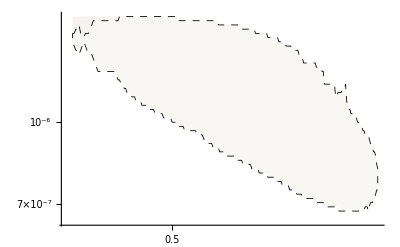

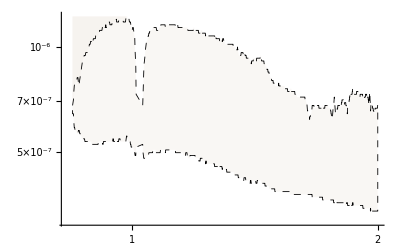

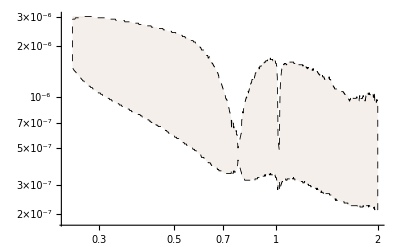

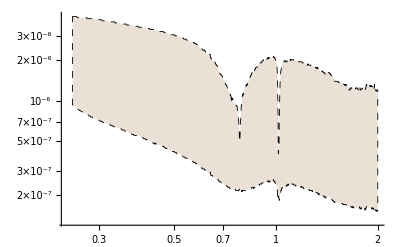

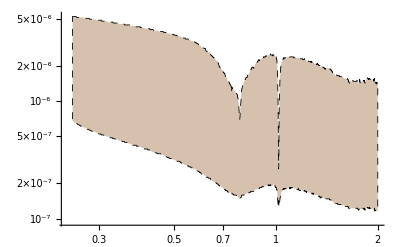

Blend::arg: RGBColor[0, 1, 1] is not a valid list of colors or images, or pairs of a real number and a color or an image.

Import::nffil: File not found during Import. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/Import/nffil",
ButtonNote->"Import::nffil"]

```mathematica
ATLAS20145a = Import["data2014/g_ATLAS5a.txt","Table"];
ATLAS20145aplot = ListLogLogPlot[ATLAS20145a,Joined->True,PlotStyle->{(*Lighter[Brown,0.9]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.9]]]
ATLAS20145b = Import["data2014/g_ATLAS5b.txt","Table"];
ATLAS20145bplot = ListLogLogPlot[ATLAS20145b,Joined->True,PlotStyle->{(*Lighter[Brown,0.9]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.9]]]
ATLAS201410 = Import["data2014/g_ATLAS10.txt","Table"];
ATLAS201410plot = ListLogLogPlot[ATLAS201410,Joined->True,PlotStyle->{(*Lighter[Brown,0.8]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.8]]]
ATLAS201420 = Import["data2014/g_ATLAS20.txt","Table"];
ATLAS201420plot = ListLogLogPlot[ATLAS201420,Joined->True,PlotStyle->{(*Lighter[Brown,0.6]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.6]]]
ATLAS201440 = Import["data2014/g_ATLAS40.txt","Table"];
ATLAS201440plot = ListLogLogPlot[ATLAS201440,Joined->True,PlotStyle->{(*Lighter[Brown,0.2]*)Black,Thickness[0.0015],Dashed},Filling->{1->Top},FillingStyle->Directive[Opacity[myopacity],Lighter[Brown,0.2]]]
```

```mathematica
Clear[fticksR,fticksR2,fticksR3,PrettyExp,PrettyExpR2]
PrettyExp[x_,MAX_:2]:=If[Abs[x]≥MAX,Superscript[10,x],If[x≥0,10^x,10.^x]]
(* Axis for Epsilon versus mass: *)
fticksR[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.008,0}},{i,2,9}],{1}],{10.^x,PrettyExp[x,AMAX],{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
PrettyExpR2[x_,MAX_:2]:=If[Abs[x]>MAX,Superscript[10,2x],If[x≥0,10^x,10.^x]]
(* Axis for Epsilon^2 versus mass *)fticksR2[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{10.^(x+Log[10,i]/2)," ",{.008,0}},{i,2,10}],{1}],{10.^x,PrettyExpR2[x,AMAX],{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1/2}],1]
(* Axis for Epsilon^2 versus mass, but with y-axis labels only every 2 decades *)
fticksR3[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{If[i≤10,10.^(x+Log[10,i]/2),10.^(0.5+x+Log[10,i-10]/2)]," ",{If[i==10,0.02,0.008],0}},{i,2,20}],{1}],{10.^x,PrettyExpR2[x,AMAX],{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1}],1]
```

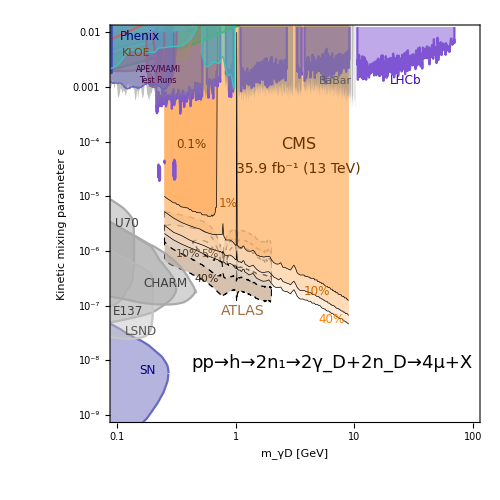

```mathematica
mylegendplot9GeV=LogLogPlot[1,{m,0.001,100},Frame->True,PlotRange->{{0.1,100},{10^-9,0.99 10^-2}},FrameTicks->{Automatic,(*fticks2[10^-11,10^-1,1]*)(*fticksR[10^-11,10^-2,0]*)Automatic},FrameLabel->{Row[{Spacer@315,"m_γD [GeV]"}],Row[{Spacer@150,"Kinetic mixing parameter ϵ"}]},LabelStyle->22,
Epilog->{
(*Inset[Style["Orsay",FontSize->12,Black],Scaled[{0.3,0.59}]],*)
(* 95% c.l. *) Inset[Style["U70",FontSize->12,Blend[{Gray,Black}]],Scaled[{0.045,0.50}]],
(* 95% c.l. *) Inset[Style["E137",FontSize->12,Blend[{Gray,Black}]],Scaled[{0.05,0.28}]],
(* 95% c.l. *) (*Inset[Style["E141",FontSize->12,Blend[{Gray,Black}]],Scaled[{0.05,0.8}]],*)
(* 95% c.l. *)(*Inset[Style["E774",FontSize->12,Blend[{Gray,Black}]],Scaled[{0.07,0.87}]],*)
(* 95% c.l. *) Inset[Style["CHARM",FontSize->12,Blend[{Gray,Black}]],Scaled[{0.15,0.35}]],
(* 5σ c.l. *) (*Inset[Style["a_(μ,  5 σ)",FontSize->12,Blend[{Cyan,Black}]],Scaled[{0.2,0.96}]],*)
(* 95% c.l. band *)(*Inset[Rotate[Style["a_(μ, ±2σ) favored",FontSize->12,Blend[{Green,Black}]],5°],Scaled[{0.11,0.89}]],*)
(* 95% c.l. *)Inset[Style["Phenix",FontSize->12,Blend[{Blue,Black}]],Scaled[{0.08,0.97}]],
(* 95% c.l. *)(*Inset[Style["a_e",FontSize->12,Blend[{Red,Black}]],Scaled[{0.1,0.86}]],*)
(* 95% c.l. *) Inset[Style["BaBar",FontSize->11, Darker[Gray,0.3]],Scaled[{0.61,0.86}]],
(* 95% c.l. *) Inset[Style["CMS",FontSize->16,Darker[Orange,0.6]],Scaled[{0.51,0.70}]],
(* 95% c.l. *) Inset[Style["35.9 fb^-1 (13 TeV)",FontSize->14,Darker[Orange,0.6]],Scaled[{0.51,0.64}]],
(* 95% c.l. *) Inset[Style["LHCb",FontSize->12,Blend[{Blue,Purple}]],Scaled[{0.80,0.86}]],
Inset[Style["0.1%",FontSize->12,(*Blend[{Purple,Black}]*)Darker[Orange,0.5]],Scaled[{0.22,0.70}]],
Inset[Style["1%",FontSize->12,(*Blend[{Purple,Black}]*)Darker[Orange,0.3]],Scaled[{0.32,0.55}]],
Inset[Style["10%",FontSize->12,(*Blend[{Purple,Black}]*)Darker[Orange,0.2]],Scaled[{0.56,0.33}]],
Inset[Style["40%",FontSize->12,(*Blend[{Purple,Black}]*)Darker[Orange,0.0]],Scaled[{0.60,0.26}]],
(* 95% c.l. *) Inset[Style["ATLAS",FontSize->14,Lighter[Brown,0.05]],Scaled[{0.36,0.28}]],
Inset[Style["40%",FontSize->11,(*Blend[{Purple,Black}]*)Darker[Brown,0.6]],Scaled[{0.26,0.36}]],
Inset[Style["10%",FontSize->11,(*Blend[{Purple,Black}]*)Darker[Brown,0.4]],Scaled[{0.21,0.425}]],
Inset[Style["5%",FontSize->11,(*Blend[{Purple,Black}]*)Darker[Brown,0.2]],Scaled[{0.27,0.425}]],
(* 95% c.l. *) (*Inset[Style["√s=13 TeV",FontSize->14,FontFamily->"Arial",Darker[Orange,0.6]],Scaled[{0.52,0.63}]],*)
(* 95% c.l. *) Inset[Style["pp→h→2n_1→2γ_D+2n_D→4μ+X",FontSize->18,FontFamily->"Arial",Blend[{Black,Black}]],Scaled[{0.60,0.15}]],
(* 95% c.l. *) Inset[Style["KLOE",FontSize->11,Blend[{Orange,Black}]],Scaled[{0.07,0.93}]],
(* 95% c.l. *) Inset[Style["SN",FontSize->12,Blend[{Blue,Black}]],Scaled[{0.10,0.13}]],
(* 95% c.l. *) Inset[Style["LSND",FontSize->12,Blend[{Lighter[Gray],Black}]],Scaled[{0.085,0.23}]],
(* 95% c.l. *) Inset[Style["APEX/MAMI",FontSize->8,Blend[{Purple,Black}],Background->None],Scaled[{0.13,0.89}]],
(* 95% c.l. *) Inset[Style["Test Runs",FontSize->8,Blend[{Purple,Black}],Background->None],Scaled[{0.13,0.86}]]
 (*Inset[Style["Test Runs",FontSize->9,Blend[{Purple,Black}],Background->None],Scaled[{0.13,0.86}]]*)
(* 95% c.l. *) (*Inset[Style["Orsay",FontSize->12,Blend[{Gray,Black}]],Scaled[{0.05,0.75}]]*)
}];
mycomboplot9GeV=Show[mylegendplot9GeV,ATLAS201440plot,(*ATLAS201420plot,*)ATLAS201410plot,ATLAS20145aplot,ATLAS20145bplot,CMS201440plot(*CMS201420plot*),CMS201410plot,(*CMS20145plot,*)CMS20141plot,CMS201401plot,LHCb2018plot,LHCb2018longlived1plot,LHCb2018longlived2plot,LHCb2018longlived3plot,LHCb2018longlived4plot,aμ2σBandplot,aμlimit5σplot,snplot,e137plot,e141plot,e774plot,orsayplot,U70plot,KLOE2012conservativeplot(*,KLOE2012optimisticplot*),(*Babar1plot*)babar2014PlotNoLines,A12011plot,apex2011plot,(*ae90cllimitplot,*)lsndplot,(*ae95cllimitplot*)ae3σlimitplot2014,charmplot,phenix2014plot,Mainz2014Plot,Hades2013Plot,KLOE2014plot(*,modelindependentplot, wasacosy2010plot*)
(*,snplotL,e137plotL,e141plotL,e774plotL(*,orsayplotL*),A12011plotL,U70plotL,KLOE2012conservativeplotL(*,KLOE2012optimisticplotL*),Babar1plotL,apex2011plotL,aμlimit5σplotL,ae95cllimitplotL(*,ae90cllimitplotL*)(*,ae5σlimitplotL*),aμ2σBandplotL,lsndplotL(*,modelindependentplotL*)(*,wasacosy2010plotL*)
,charmplot*),ImageSize->500,AspectRatio->1.0]
Export["plots/AllConstraints-11-14-12.pdf",mycomboplot9GeV/.{EdgeForm[],RGBColor[i1_,i2_,i3_],i_}:>{EdgeForm[RGBColor[i1,i2,i3]],RGBColor[i1,i2,i3],i}];
```

```mathematica
Export["/Users/Alfredo/Desktop/limite_DarkSUSY_2018/Limit_DarkPhoton_Epsilon_vs_mass_compExperiments_logmass_9GeV_90CL_2018.pdf",mycomboplot9GeV]
```

/Users/Alfredo/Desktop/limite_DarkSUSY_2018/Limit_DarkPhoton_Epsilon_vs_mass_compExperiments_logmass_9GeV_90CL_2018.pdf

```mathematica
Export["/Users/Alfredo/Desktop/limite_DarkSUSY_2018/Limit_DarkPhoton_Epsilon_vs_mass_compExperiments_logmass_9GeV_90CL_2018.eps",mycomboplot9GeV]
```

/Users/Alfredo/Desktop/limite_DarkSUSY_2018/Limit_DarkPhoton_Epsilon_vs_mass_compExperiments_logmass_9GeV_90CL_2018.eps

```mathematica
Export["/Users/Alfredo/Desktop/limite_DarkSUSY_2018/Limit_DarkPhoton_Epsilon_vs_mass_compExperiments_logmass_9GeV_90CL_2018.png",mycomboplot9GeV]
```

/Users/Alfredo/Desktop/limite_DarkSUSY_2018/Limit_DarkPhoton_Epsilon_vs_mass_compExperiments_logmass_9GeV_90CL_2018.png